## 函数定义

```mathematica
CountBox=Compile[{{im,_Integer,2},{t,_Integer},{Bl,_Integer}},Module[{l,fl,cnt},
l=2^t;
fl=Table[0,{i,2*l-1},{j,2*l-1}];
cnt=Table[0,{k,t+1}];
Do[If[im[[i,j]]==Bl,Module[{ii,jj},
ii=i+l-1;jj=j+l-1;
Do[
fl[[ii,jj]]=1;
ii=Quotient[ii,2];
jj=Quotient[jj,2];
,{k,t+1}]
]],{j,l},{i,l}];
Do[cnt[[k]]+=fl[[i,j]],{k,t+1},{i,2^(k-1),2^k-1},{j,2^(k-1),2^k-1}];
cnt],CompilationTarget->"C"];
```

```mathematica
CountBoxTrans=Compile[{{a,_Real,3},{b,_Real,2},{c,_Real,2},{d,_Real,1},{l,_Integer},{t,_Integer},{cut,_Integer,1},{lc,_Integer},{nm,_Integer},{nml,_Integer}},
Module[{pts,pa,pb,cnt,mxx,mnx,mxy,mny,st,nx,ny,nn,ans,ml},
pts=Table[.0,{n,nm*l},{x,2}];
st=Table[10^9,{n,nm*l},{x,2}];
ans=Table[.0,{n,lc*nml},{x,2}];
pa=1;pb=2;cnt=1;
Do[Do[Do[
pts[[pb,1]]=a[[j,1,1]]*pts[[pa,1]]+a[[j,1,2]]*pts[[pa,2]]+b[[j,1]];
pts[[pb,2]]=a[[j,2,1]]*pts[[pa,1]]+a[[j,2,2]]*pts[[pa,2]]+b[[j,2]];
pts[[pb,1]]/=c[[j,1]]*pts[[pa,1]]+c[[j,2]]*pts[[pa,2]]+d[[1]];
pts[[pb,2]]/=c[[j,1]]*pts[[pa,1]]+c[[j,2]]*pts[[pa,2]]+d[[1]];
pb+=1
,{j,l}];
pa+=1
,{i,cnt}];
cnt=pb-pa;
,{k,t}];
pb-=1;mnx=10.^9;mny=10.^9;mxx=-10.^9;mxy=-10.^9;
Do[
mxx=Max[mxx,pts[[i,1]]];
mxy=Max[mxy,pts[[i,2]]];
mnx=Min[mnx,pts[[i,1]]];
mny=Min[mny,pts[[i,2]]];
,{i,pa,pb}];
ml=Max[mxx-mnx,mxy-mny];
Print["Points:",pb-pa];
Do[
nn=cut[[j]]^i;
Do[
nx=Floor[nn(pts[[k,1]]-mnx)/ml];
ny=Floor[nn(pts[[k,2]]-mny)/ml];
(*If[nx==nn,nx-=1];If[ny==nn,ny-=1];*)
st[[k-pa+1,1]]=nx;st[[k-pa+1,2]]=ny;
,{k,pa,pb}];
ans[[i*lc-lc+j,2]]=N[Log[Length[Union[st]]-1]];
ans[[i*lc-lc+j,1]]=-N[Log[ml/nn]];
,{i,nml},{j,lc}];
ans
],
CompilationTarget->"C"
];
```

```mathematica
FracParaEsti[x_]:=Module[{t,i},t=Table[{n,Module[{fs,l,tt},
fs=Fourier[Iminit[x,n]];
l=Dimensions[fs][[1]]/2;
tt=Take[fs,{l-3,l},{l-3,l}];
Mean[Flatten[Abs[tt]*2^(n-4)]]
]}
,{n,6,12}];
For[i=6,i<12 && t[[i-4,2]]>t[[i-5,2]],i++];
{ListLinePlot[t],i+1}
];
```

```mathematica
SimTrans[s_,fp_]:=Module[{mat},
mat=If[MatrixQ[s],s,ScalingMatrix[Table[s,Length[fp]]]];
AffineTransform[{mat,fp-mat.fp}]];
Iminit[x_,t_:10]:=Module[{im,l},
l=2^(t+1);
im=Show[x,ImageSize->{l,l}];
ImageData[Binarize[Rasterize[im,RasterSize->{2^t,2^t}]]]
]
Options[ImgFracDim]={MaxIterations->Automatic,Background->0};
ImgFracDim[a_,opts:OptionsPattern[]]:=Module[{t,b,im,ls,lm},
t=OptionValue[MaxIterations];
b=OptionValue[Background];
If[t==Automatic,t=11];
im=Iminit[a,t];
ls=Log2[CountBox[im,t,b]];
lm=LinearModelFit[ls,dim,dim,Weights->Automatic];
{Plot-> Show[ListPlot[ls],Plot[{lm[x]},{x,0,t+1}]],"Dimension"->lm["BestFitParameters"][[2]],"Error"->lm["ParameterErrors"][[2]],"P-Value"->lm["ParameterPValues"][[2]],"Inteval"->lm["ParameterConfidenceIntervals"][[2]]}
];
Options[FracDim]={MaxIterations->-1,Point->10^6,List->{2,3,5,7,11,13,17,19}};
FracDim[a_,opts:OptionsPattern[]]:=Module[{ti,nm,ls,Ma,b,c,d,l,t,nml,cnt,il,lm},
ti=OptionValue[MaxIterations];
nm=OptionValue[Point];
ls=OptionValue[List];
Ma=Map[#["AffineMatrix"]&,a];
b=Map[#["AffineVector"]&,a];
c=Map[#["FractionalVector"]&,a];
d=Map[#["FractionalConstant"]&,a];
l=Length[Ma];
If[ti==-1,t=Floor[Log[l,nm(l-1)+1]],t=Min[ti,Floor[Log[l,nm(l-1)+1]]]];

nml=Floor[Log[Max[ls],nm]]-2;
cnt=CountBoxTrans[Ma,b,c,d,l,t,ls,Length[ls],nm,nml];
il=cnt;
lm=LinearModelFit[il,dim,dim,Weights->Automatic];
{Plot-> Show[ListPlot[il],Plot[{lm[x]},{x,0,Max[#[[1]]&/@il]+1}]],"Dimension"->lm["BestFitParameters"][[2]],"Error"->lm["ParameterErrors"][[2]],"P-Value"->lm["ParameterPValues"][[2]],"Inteval"->lm["ParameterConfidenceIntervals"][[2]]}
]
```

## 样例

Iminit将图像变成便于计算的二值初始格式，第二个参数是图像的大小，例如设为10，图像长宽是1024。

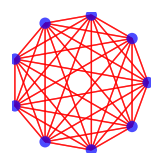
```mathematica
pse=Iminit[-Graphics-,10];
```

Iminit的输出是二维01矩阵

```mathematica
Take[pse,{405,415},{400,410}]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

长宽是1024

```mathematica
Dimensions[pse]
```

{1024,1024}

查看转换后的图像

```mathematica
pse//Image[#,ImageSize->Small]&
```

-Graphics-

转换后的图像有时候比原图像精细或粗糙，取决于设定的维数。

ImgFracDim通过输入图像和计算精度给出图像的维度估计，使用的方法是BoxCount根据BoxSize的双对数线性估计
将DrawFrac生成的图像放里面

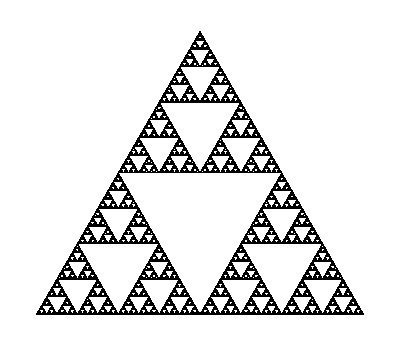
```mathematica
ImgFracDim[-Graphics-,MaxIterations->10]
```

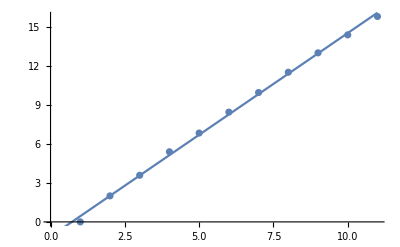
{Plot→-Graphics-,Dimension→1.56478,Error→0.0211532,P-Value→7.62518×10^-14,Inteval→{1.51693,1.61263}}

Plot表示拟合图像，Dimension表示估计维数，Error和P-Value表示拟合的估计范围和P值

```mathematica
(Log[3]/Log[2])//N
```

1.58496

维度与实际维度计算的误差来自于生成时的迭代层数限制，以及图像计算BoxCount时的精度误差，基本上可以说图像的精度影响计算维数的精度。

使用生成分形的图像时，ImgFracDim不是精度设置的越高越好，推荐的方法是用二值化后的图像查看作为参考。
用如下方法显示图像参数取10和12的部分截取结果

```mathematica
{Iminit[-Graphics-,10]//Image//ImageCrop[#,{200,200}]&,
Iminit[-Graphics-,12]//Image//ImageCrop[#,{200,200}]&}
```

{-Graphics-,-Graphics-}

注意到选用高精度的图像确实提升了图像的细节，但是分形的结构在参数取12的部分没有跟得上像素的精细程度，
程序会认为最里面的三角形是实心的，从而实际上使得计算的维度偏高，一般来说取10都是较好的选择。

FracParaEsti使用傅里叶变换估计应该使用的参数，方法是选择高频区域的谱的第一个下降峰，此时可以认为细节不会继续变多。
该方法不在默认参数选择。
该方法对样例图片的参数建议是9。

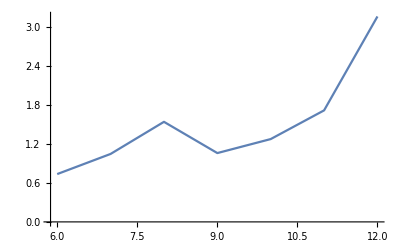
{-Graphics-,9}

```mathematica
ll=FracParaEsti[-Graphics-]
```

FracDim对分式线性变换组合做维数估计，输入是TransformationFunction序列

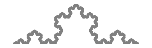
-Graphics-：1.26186

```mathematica
vcurve={AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,0}}],AffineTransform[{RotationMatrix[Pi/3].ScalingMatrix[{1/3,1/3}],{1/3,0}}],AffineTransform[{RotationMatrix[-Pi/3].ScalingMatrix[{1/3,1/3}],{1/2,Sqrt[3]/6}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,0}}]};
```

Points:1048575

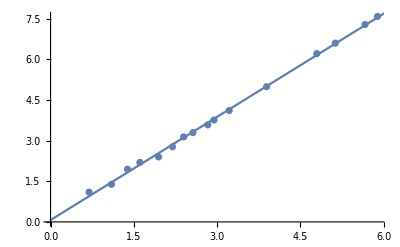
{Plot→-Graphics-,Dimension→1.26991,Error→0.0130266,P-Value→3.12345×10^-21,Inteval→{1.24197,1.29785}}

```mathematica
FracDim[vcurve]
```

:1.58496

Points:1594322

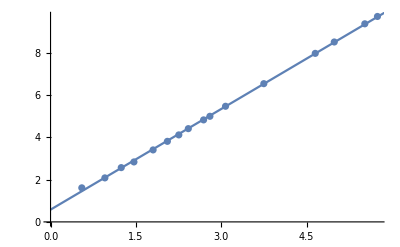
{Plot→-Graphics-,Dimension→1.58586,Error→0.00820407,P-Value→2.1661×10^-25,Inteval→{1.56826,1.60345}}

```mathematica
strig={AffineTransform[{ScalingMatrix[{1/2,1/2}],{0,1/2}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]};
FracDim[strig]
```

:

Points:1594322

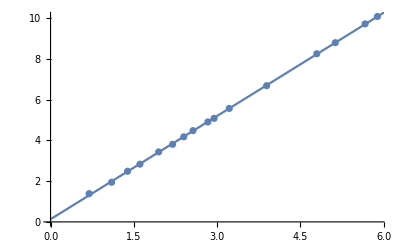
{Plot→-Graphics-,Dimension→1.68836,Error→0.00477396,P-Value→4.60795×10^-29,Inteval→{1.67812,1.6986}}

```mathematica
astrig={SimTrans[((Sqrt[5]-1)/2)^2,{0,Sqrt[3]/2}],
SimTrans[((Sqrt[5]-1)/2),{-1/2,0}],
SimTrans[((Sqrt[5]-1)/2),{1/2,0}]
};
FracDim[astrig]
```

## 参数

ImgFracDim的参数：MaxIterations表示最大迭代次数，默认是11；Background表示背景颜色，取0或1，默认取0；
FracDim的参数：Point表示点的多少，默认计算约10^6个点，MaxIterations表示最大迭代次数，默认与Point一致，List->{2,3,5,7,11,13,17,19}表示Box分划的格子数，默认取20以下的质数。